```mathematica
SetDirectory["/Users/penn/Documents/Code/Github/My_Lib/Mathematica_Lib/Machine Learning/H5"];
data1=Import["dataset1","Table"];
rdata1=RandomSample[data1];
```

```mathematica
KMeans[k_,data_]:=
Module[{Renew,Label,Iteration},
clusters=RandomSample[data,k];
Label[clusters_]:=Flatten[Table[Ordering[Table[EuclideanDistance[data[[i]],clusters[[j]]],{j,Length[clusters]}],1],{i,Length[data]}]];
Renew[labels_]:=
Module[{position},
position=PositionIndex[labels];
Return[Table[Mean[data[[position[[i]]]]],{i,Length[position]}]]];
Iteration[labels_,clusters_]:=
Module[{newlabels,newclusters},
newclusters=Renew[labels];
newlabels=Label[newclusters];
If[newlabels==labels,labels,Iteration[newlabels,newclusters]]];
Return[Iteration[clusters,Label[clusters]]]]
```

```mathematica
InitialTryKMeans[k_,data_,labels_,times_]:=
Module[{best,Try},
best=KMeans[k,data];
Try[t_]:=If[t==0,best,Module[{new},new=KMeans[k,data];If[EuclideanDistance[new,labels]<EuclideanDistance[best,labels],best=new;Try[t-1],Try[t-1]]]];
Return[Try[times]]]
```

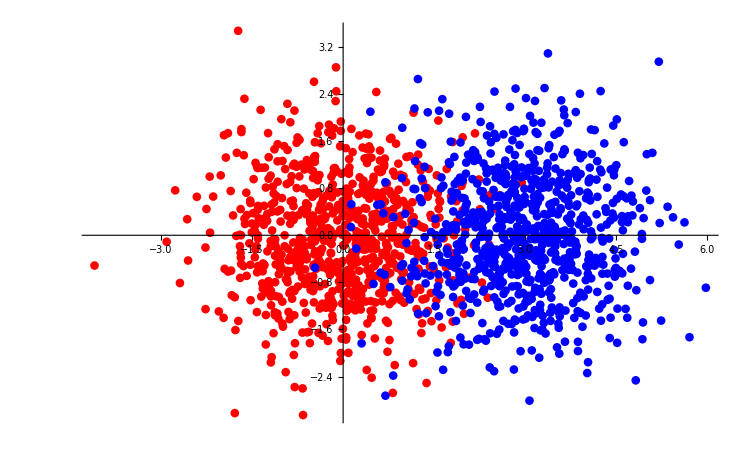

```mathematica
Show[ListPlot[Part[data1,1;;800],PlotStyle->Red],ListPlot[Part[data1,801;;1600],PlotStyle->Blue],PlotRange->All]
```

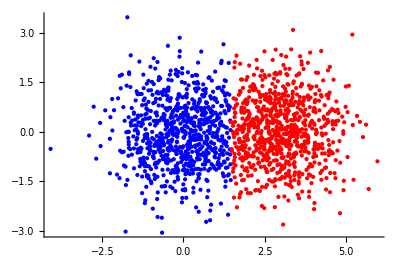

```mathematica
Show[Table[If[z[[i]]==1,Graphics[{Red,Point[rdata1[[i]]]}],Graphics[{Blue,Point[rdata1[[i]]]}]],{i,1,Length[z]}],Axes->True]
```

```mathematica
z[[1]]
```

1

```mathematica
z[[2]]==1
```

True

```mathematica
z=KMeans[2,rdata1];
```

```mathematica
z
```

{1,1,2,1,1,2,1,1,2,1,1,1,2,1,2,1,1,2,1,2,1,2,2,2,2,2,1,2,2,2,1,1,1,1,2,1,1,2,1,1,2,2,1,1,2,2,1,1,2,1,2,2,2,2,2,1,1,1,2,1,2,1,2,2,1,1,2,2,1,2,1,2,1,2,2,1,2,2,2,2,2,1,2,2,2,1,2,1,1,2,1,1,2,2,1,2,2,2,2,2,1,1,1,1,2,2,2,2,1,2,2,1,2,1,2,1,1,1,2,2,2,1,2,2,2,2,1,1,1,2,2,2,1,2,1,1,1,1,2,2,1,2,2,2,1,1,1,1,2,1,2,1,1,1,1,2,1,2,2,1,1,2,2,1,1,1,2,1,2,1,1,1,2,1,2,2,1,1,2,1,2,1,2,1,2,2,1,1,1,2,1,1,1,1,2,2,1,2,2,1,1,2,1,2,1,1,2,2,1,1,2,1,1,1,1,1,2,1,2,1,1,1,2,1,1,2,1,1,1,2,1,1,1,2,1,2,2,1,1,1,2,1,1,1,1,2,2,2,2,2,2,1,1,1,1,1,1,2,1,2,1,2,1,2,1,1,2,2,2,2,2,2,2,1,2,2,1,1,2,2,1,2,1,1,1,2,2,2,1,2,1,2,1,1,1,2,1,1,1,1,2,1,2,2,2,1,2,1,2,2,2,2,2,1,2,1,2,2,2,2,1,1,1,1,2,1,2,2,1,2,1,1,1,1,2,2,2,2,1,1,1,1,2,2,2,2,2,2,1,2,2,1,2,2,2,1,1,2,2,1,1,1,2,2,1,1,2,1,1,1,2,2,2,2,1,1,1,1,2,2,2,2,1,2,1,1,2,1,2,1,2,2,2,2,2,1,1,2,2,1,1,1,1,1,2,1,2,2,2,2,1,2,1,2,2,2,2,1,2,2,2,2,1,2,1,2,1,2,1,2,2,1,1,2,2,2,1,2,1,2,2,1,1,1,2,1,1,2,1,1,2,2,2,2,1,2,2,1,1,2,1,1,2,2,1,2,2,1,1,2,1,1,1,2,1,1,2,2,1,2,1,2,1,2,1,2,1,2,1,1,2,1,2,2,1,1,1,2,1,2,1,1,1,2,1,2,2,2,1,2,2,2,1,2,2,1,1,2,1,1,2,1,2,1,1,1,2,1,2,1,2,1,1,2,2,1,2,1,2,1,1,2,2,1,1,2,1,1,2,1,2,1,2,2,1,2,1,2,2,1,1,2,1,1,2,2,2,2,2,1,2,1,1,1,2,1,1,1,1,1,2,1,1,1,2,1,2,2,1,1,2,1,2,2,2,1,2,1,2,2,1,1,2,2,1,2,2,1,2,1,1,1,2,2,2,1,1,2,1,2,2,1,2,1,1,2,2,1,2,1,2,2,2,2,1,2,2,1,1,1,1,2,1,2,2,2,2,1,2,2,1,1,1,1,1,1,2,1,2,1,1,1,2,2,2,1,1,2,1,1,2,2,2,1,2,1,2,1,2,2,1,2,1,2,1,1,1,1,1,1,2,1,1,2,1,2,2,1,1,2,2,1,1,2,2,2,2,2,1,1,1,2,1,1,2,1,1,2,1,1,2,1,1,1,2,1,2,2,1,2,1,1,1,1,2,2,2,1,2,2,2,2,1,2,1,1,2,2,2,2,1,2,1,2,1,2,2,2,2,1,2,1,1,1,2,1,2,1,2,1,2,2,2,1,2,2,2,2,2,1,1,1,2,2,1,2,2,1,2,1,1,2,2,2,2,2,1,1,1,2,1,1,2,1,1,2,1,1,1,1,1,2,2,2,2,2,1,2,2,2,2,1,1,1,1,2,2,1,1,1,1,2,2,2,1,2,1,2,1,1,1,2,2,1,1,2,1,2,2,1,2,2,1,1,2,2,2,2,1,2,2,2,2,1,1,2,1,2,1,1,1,2,2,2,2,2,2,2,1,2,2,1,1,1,1,1,2,1,2,2,2,1,2,1,1,2,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,2,2,1,1,1,1,2,1,1,1,2,2,2,1,1,2,2,1,1,2,2,1,2,2,2,2,2,2,1,1,1,2,1,2,2,2,1,1,2,2,1,1,1,1,2,1,2,2,1,2,2,2,2,1,2,2,2,2,2,2,2,1,2,1,2,1,2,2,1,1,2,1,1,2,2,2,1,1,1,2,2,2,1,2,1,2,2,1,2,1,2,1,1,2,2,2,2,2,1,2,1,2,2,2,1,2,1,1,1,2,2,1,1,1,2,2,2,2,2,1,1,1,2,2,2,2,2,1,1,2,2,1,2,2,1,1,2,2,1,1,2,2,2,2,1,1,1,1,2,2,1,1,1,1,2,2,1,1,2,1,2,1,2,2,1,1,2,1,1,2,2,1,1,2,1,2,2,1,2,1,1,1,1,2,1,1,1,1,2,2,2,1,1,1,1,2,2,1,1,1,1,1,2,2,2,2,1,1,2,1,1,1,1,2,2,1,1,1,1,2,2,2,1,1,1,2,2,2,1,2,2,2,2,1,2,2,1,1,1,1,1,1,1,2,2,2,1,1,2,2,1,1,2,2,1,2,1,1,2,1,1,1,2,1,1,1,2,2,2,1,2,2,1,2,1,2,2,1,2,2,1,1,2,2,1,1,2,1,2,1,1,1,2,2,2,2,1,2,2,1,1,2,2,1,2,2,1,1,2,1,1,1,2,2,2,2,1,1,1,1,2,1,1,2,1,1,1,2,2,1,2,2,2,2,1,1,2,2,1,2,1,1,2,2,1,2,1,1,1,1,2,2,2,1,2,1,1,1,2,2,2,2,2,2,1,1,2,1,2,2,1,1,2,2,1,1,2,2,2,1,2,2,1,2,1,1,1,1,1,1,2,2,1,1,2,1,2,1,1,1,1,1,2,2,1,2,1,2,2,2,2,2,2,2,1,2,2,1,2,1,2,2,1,2,2,1,1,2,2,2,1,2,2,1,2,1,1,2,2,2,1,2,1,1,2,1,1,2,1,1,2,1,2,2,2,2,1,1,2,1,1,1,2,2,1,2,1,1,2,2,1,2,1,2,1,1,1,2,1,2,1,1,1,1,2,1,2,1,1,2,1,1,2,1,1,1,1,2,2,1,1,2,2,1,1,1,2,2,2,2,2,2,2,1,2,2,2,2,1,2,1,2,1,1,2,1,2,2,1,1,1,1,1,1,1,2,1,2,1,1,1,2,2,1,1,2,2,2,1,2,1,1,1,2,2,1,1,2,1,2,1,1,1,1,2,1,1,2,1,1,2,2,1,2,1,2,2,2,2,1,1,1,2,1,1,2,2,1,2,2,1,1,1,2,2,2,1,2,1,1,2,2,2,2,2,1,2,2,1,2,1,1,1,2,2,1,1,2,1,1,2,2,2,1,1,1,1,1,2,1,2,1,2,2,2,1,1,2,2,1,1,2,2,2,2,2,2,1,1,1,1,2,1,2,1,1,2,1,2,1,1,2,2,1,1,1,2,2,1,1,2,1,2,2,2,2,2,1,2,1,2,1,1,1,2,1,2,2,1}